```mathematica
L=30;
κ=1;β=1;
γ1=2;γ2=0.5;
A1=0.1;B1=0.05;
```

```mathematica
tmax=100;
```

```mathematica
a=1;c=2;
```

```mathematica
gauss[x_,b_]:=a Exp[-(x-b)^2/(2 c^2)]
```

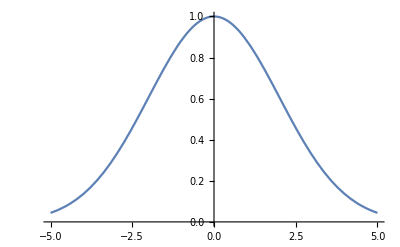

```mathematica
Plot[gauss[x,0],{x,-5,5}]
```

```mathematica
sol=NDSolve[{
D[u[x,t],t]==D[u[x,t],{x,2}]+u[x,t](1-u[x,t]-γ1 v[x,t]),
D[v[x,t],t]==κ D[v[x,t],{x,2}]+β v[x,t](1-v[x,t]-γ2 u[x,t]),
u[-L,t]==0, u[L,t]==0,v[-L,t]==0,v[L,t]==0,
u[x,0]==gauss[x,-10],v[x,0]==gauss[x,10]},
{u,v},
{x,0,L},
{t,0,tmax}]
```

{{u→InterpolatingFunction[…],v→InterpolatingFunction[…]}}

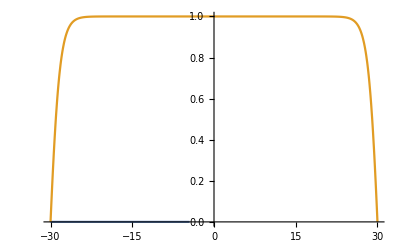

```mathematica
Plot[{Evaluate[u[x,tmax]/.sol],Evaluate[v[x,tmax]/.sol]},{x,-L,L},PlotRange->{0,1}]
```

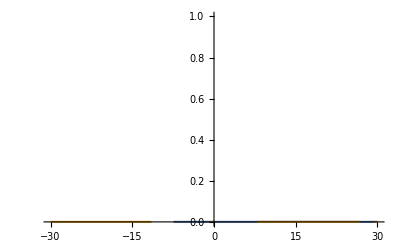

```mathematica
Plot[{Evaluate[D[u[x,t]/.sol,t]/.t->tmax],
Evaluate[D[v[x,t]/.sol,t]/.t->tmax]},{x,-L,L},PlotRange->{0,1}]
```

```mathematica
xPoints=Range[-L,L,2L/100];
uPoints=Evaluate[u[xPoints,tmax]/.sol][[1]];
vPoints=Evaluate[v[xPoints,tmax]/.sol][[1]];
dudtPoints=Evaluate[D[u[xPoints,t]/.sol,t]/.t->tmax][[1]];
dvdtPoints=Evaluate[D[v[xPoints,t]/.sol,t]/.t->tmax][[1]];
```

```mathematica
uvPoints={N[xPoints],uPoints,vPoints,dudtPoints,dvdtPoints};
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["./spatial-competitive-lotka-volterra-1-3.csv",uvPoints]
```

./spatial-competitive-lotka-volterra-1-3.csv